Task 1.1
Task 1.1a

h = 0

```mathematica
h=0;
r=0;
roots=Solve[h+x(r-x)==0,x];
roots = x/. roots;
txt = Text["Unstable", {.7,.7}];
Plot[h+x(r-x),{x,-10,10}, Epilog->{Black,PointSize@Large,Point[{{Part[roots,1],0},{Part[roots,2],0}}]}];
```

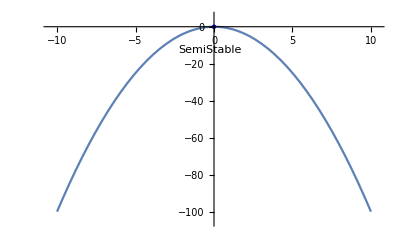

h  > 0

```mathematica
h=5;
r=0;
roots=Solve[h+x(r-x)==0,x];
roots = x/. roots;

Show[ListPlot[{{{roots[[1]],0}},{{roots[[2]],0}}},PlotMarkers->{Style[○,Black,20],Style[●,Black,20]},PlotRange->{{-10,10},{-10,10}}],Plot[h+x(r-x),{x,-10,10},PlotStyle->{{ColorData[97][1],Thick}}],ImageSize->Large];
```

h < 0

```mathematica
h=-5;
r=0;
roots=Solve[h+x(r-x)==0,x];
roots = rootsForX=x/. roots;
Plot[h+x(r-x),{x,-10,10}];
```

Task 1.1b

```mathematica
ContourPlot3D[h+x(r-x)==0,{x,-10,10},{h,-10,10},{r,-10,10}];
```

Task 1.1c

```mathematica
x=.
r=.
h=.
xstar=.
prim =.

f[x_]:= h + x (r - x)
prim = f'[x];
xstar = x/. Solve[prim == 0, x];
hc = h /. Solve[f[xstar] == 0, h]
```

{-r^2/4}

Task 1.1 d

```mathematica
M = {{1,-1},{0,1}};
Eigenvectors[M];
```

{{1,0},{0,0}}

1.2 Subcritical pitchfork
1.2a

```mathematica
r=.
x=.
f[x_] := r*x+4x^3-9x^5;
roots= x/.Solve[f'[x]==0,x];
g[r_]:=roots[[4]];
rc = Solve[f[g[r]]==0,r]

p1= Plot[{roots},{r,-2,2},PlotStyle->{{Black,Dashing[Tiny]},{Black,Dashing[Tiny]},{Black,Line},{Black,Line}}];
p2 = Plot[{0},{r,-2,0},PlotStyle->{Black}];
p3 = Plot[{0},{r,0,2},PlotStyle->{Black,Dashing[Tiny]}];
Show[p1,p2,p3];
```

{{r→-4/9}}

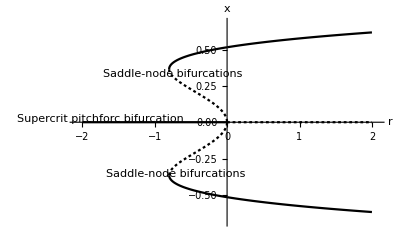

```mathematica
Show[%2586,AxesLabel->{HoldForm[r],HoldForm[x]},PlotLabel->None,LabelStyle->{GrayLevel[0]}];
```

```mathematica
Manipulate[Plot[r*x+4x^3-9x^5,{x,-1,1}],{r,-1,1}];
```

TASK 1.3

```mathematica
sigma=.
ClearAll[x]
ClearAll[y]


M = {{sigma+3,4},{-9/4,sigma-3}}
Eigenvalues[M];
-Eigenvectors[M][[1]];
Inverse[M];

M = {{sigma+3,4},{-9/4,sigma-3}}
plot ={M[[1,1]]x+M[[1,2]]y,M[[2,1]]x+M[[2,2]]y}

st1 =StreamPlot[plot /. sigma ->-1,{x,-3,3},{y,-3,3},PlotLabel->"Stable for sigma=-1"];
st2 =StreamPlot[plot /. sigma ->0,{x,-3,3},{y,-3,3},PlotLabel->"Uniform motion for sigma=0"];
st3 =StreamPlot[plot /. sigma ->1,{x,-3,3},{y,-3,3},PlotLabel->"Unstable sigma=1"];
GraphicsRow[{st1,st2,st3}];

sigma = .;
c = 3/2;
d=-2;
K ={{sigma-c d, 4},{-9/4, sigma-3}}
Eigenvalues[K]

sigma = 0;
c=.;
d=.;
K ={{sigma-c d, d^2},{-c^2, sigma+c d}};
Eigenvectors[K]
```

{{3+sigma,4},{-9/4,-3+sigma}}

{{3+sigma,4},{-9/4,-3+sigma}}

{(3+sigma) x+4 y,-(9 x)/4+(-3+sigma) y}

{{3+sigma,4},{-9/4,-3+sigma}}

{sigma,sigma}

{{d/c,1},{0,0}}

{{3+sigma,4},{-9/4,-3+sigma}}

{sigma,sigma}

{{d/c,1},{0,0}}

```mathematica
Task 1.4
```

1.4b)	Generate the function for x and y for x0 and y0

```mathematica
sigma =.;t=.; x=.;y=.;sol=.;x0=.;y0=.;u=.;v=.;
ClearAll[y]
ClearAll[x]
x0=u;
y0=v;
sol[x0_,y0_]:=DSolve[{x'[t] ==((sigma+1)x[t]+3y[t]) , y'[t] ==(-2x[t]+(sigma-1)y[t]), x[0]==x0,y[0]==y0},{x,y},{t}];
sol[x0,y0]
```

{{x→Function[{t},1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])]}}

Case: Sigma = 0

```mathematica
t=.
min=-2;
max=2;
dist=10;
sigma=0;
u=1;
v=1;
sol[x0,y0]


M = {{sigma+1, 3}, {-2, sigma-1}};
Re[Eigenvalues[M]];

inits =Join[Table[ {min,y},{y,min,max,dist}],Table[ {max,y},{y,min,max,dist}],
Table[ {x,min},{x,min,max,dist}],
Table[ {x,max},{x,min,max, dist}]];


text = Graphics[Text["Undamped for sigma = 0", {.3,.7}]];
plot1= Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,50}],{i,Length[inits]}],text];p1=(plot1//Normal)/.Line[x_]:>{Arrowheads[{0,0.1,0}],Arrow[x]};
```

{{x→Function[{t},1/5 (5 Cos[√5 t]+4 √5 Sin[√5 t])],y→Function[{t},1/5 (5 Cos[√5 t]-3 √5 Sin[√5 t])]}}

Case: Sigma = -1/10

```mathematica
sigma=-1/10;

M = {{sigma+1, 3}, {-2, sigma-1}};
a = Re[Eigenvalues[M]]

text = Graphics[Text[Style["Stable for sigma = -1/10",Bold, Large], {0,1}]];
plot2= Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,50}],{i,Length[inits]}],text];p2=(plot2//Normal)/.Line[x_]:>{Arrowheads[{0,-a[[1]],0}],Arrow[x]};
```

{-1/10,-1/10}

Sigma  = 1/10

```mathematica
sigma=1/10;

M = {{sigma+1, 3}, {-2, sigma-1}};
a = Re[Eigenvalues[M]]

text = Graphics[Text[Style["Unstable for sigma = 1/10",Bold, Large], {50,150}]];
plot3= Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,50}],{i,Length[inits]}],text];p3=(plot3//Normal)/.Line[x_]:>{Arrowheads[{0,a[[1]],0}],Arrow[x]};
```

{1/10,1/10}

1.4 d

```mathematica
period = 2 Pi;
argument = Sqrt[5];
periodTime = period/argument
```

(2 π)/(√5)

1.4 e

```mathematica
sigma =.;t=.; x=.;y=.;sol=.;x0=.;y0=.;u=.;v=.;a=.;
ClearAll[y]
ClearAll[x]
sigma=0;
u=1;
v=1;
x0=u;
y0=v;
sol[x0_,y0_]:=DSolve[{x'[t] ==((sigma+1)x[t]+3y[t]) , y'[t] ==(-2x[t]+(sigma-1)y[t]), x[0]==x0,y[0]==y0},{x,y},{t}]
fkn[t_] :=sol[x0,y0]

vec={ 1/5 (5 Cos[√5 t]+4 √5 Sin[√5 t]),1/5 (5 Cos[√5 t]-3 √5 Sin[√5 t])};

max=FindMaximum[Norm[vec],t];
min=FindMinimum[Norm[vec],t];
kvot = max/min
angle = Solve[Tan[theta]==kvot[[1]],theta];
angle = theta/.angle;
vec = {Sin[angle],-Cos[angle]}
```

{1.61803,{(t→0.637691)/(t→1.34017)}}

{{0.850651},{-0.525731}}